If f(x) + 2f(1/x) + 3f(x/(x-1)) == x, what is f(x)?

```mathematica
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]/Total@Array[b[#] x^#&,n+1,0]
f[x, 3]
```

(a[0]+x a[1]+x^2 a[2]+x^3 a[3])/(b[0]+x b[1]+x^2 b[2]+x^3 b[3])

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x,n]+2f[1/x,n]+3f[x/(x-1),n]==x,x]},{DeleteDuplicates@#,Length@#}&@sol]
```

```mathematica
sol[3]
```

{{{b[0]→0,b[1]→0,b[2]→0,b[3]→0},{b[3]→0,b[2]→0,b[1]→0,b[0]→0},{a[2]→-b[1]/24,a[1]→-(5 b[1])/24,a[3]→-b[1]/12,a[0]→b[1]/12,b[3]→0,b[2]→-b[1],b[0]→0},{a[2]→-b[1]/24,a[3]→-b[1]/12,a[1]→-(5 b[1])/24,a[0]→b[1]/12,b[3]→0,b[2]→-b[1],b[0]→0}},60}

```mathematica
f[x, 3]/.%[[1]][[3]]//Simplify
```

(-2+5 x+x^2+2 x^3)/(24 (-1+x) x)

```mathematica
% // Apart
```

1/8+1/(4 (-1+x))+1/(12 x)+x/12

```mathematica
(* Another: f(x)/x == f(2x) *)
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]/Total@Array[b[#] x^#&,n+1,0]
f[x, 2]
```

(a[0]+x a[1]+x^2 a[2])/(b[0]+x b[1]+x^2 b[2])

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x,n]/x==f[2 x,n],x]},{DeleteDuplicates@#,Length@#}&@sol]
```

```mathematica
sol[2]
```

{{{a[0]→0,a[2]→0,a[1]→0},{b[0]→0,b[2]→0,b[1]→0}},2}

```mathematica
f[x_,n_]:=(Total@Array[a[#] x^#&,n+1,0]+Total@Array[b[#] x^(1/#)&,n-1,2])/(Total@Array[c[#] x^#&,n+1,0]+Total@Array[d[#] x^(1/#)&,n-1,2])
f[x, 2]
```

(a[0]+x a[1]+x^2 a[2]+√x b[2])/(c[0]+x c[1]+x^2 c[2]+√x d[2])

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x,n]/x==f[2 x,n],x]},{DeleteDuplicates@#,Length@#}&@sol]
```

```mathematica
sol[2]
```

$Aborted

```mathematica
(* Another: f(x)+2 f(1/(1-x))==x 
https://www.quora.com/How-do-I-solve-f-x-+-2f-left-frac-1-1-x-right-x-for-f *)
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]/Total@Array[b[#] x^#&,n+1,0]
f[x, 2]
```

(a[0]+x a[1]+x^2 a[2])/(b[0]+x b[1]+x^2 b[2])

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x,n]+2f[1/(1-x),n]==x,x]},{DeleteDuplicates@#,Length@#}&@sol]
```

```mathematica
sol[3]
```

{{{b[0]→0,b[1]→0,b[2]→0,b[3]→0},{b[3]→0,b[2]→0,b[1]→0,b[0]→0},{a[3]→-b[1]/9,a[2]→-b[1]/3,a[1]→(2 b[1])/3,a[0]→-(4 b[1])/9,b[3]→0,b[2]→-b[1],b[0]→0}},12}

```mathematica
f[x, 3]/.%[[1]][[3]]//Simplify
```

(4-6 x+3 x^2+x^3)/(9 (-1+x) x)

```mathematica
%//Apart
```

4/9+2/(9 (-1+x))-4/(9 x)+x/9

```mathematica
(* Another: 2 f(x) + 3 f(-x)== x^2-x-1 *)
```

```mathematica
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]/Total@Array[b[#] x^#&,n+1,0]
f[x, 2]
```

(a[0]+x a[1]+x^2 a[2])/(b[0]+x b[1]+x^2 b[2])

```mathematica
sol[n_]:=With[{sol=SolveAlways[2 f[x,n]+3f[-x,n]==x^2-x-1,x]},{DeleteDuplicates@#,Length@#}&@sol]
```

```mathematica
sol[2]
```

{{{b[2]→0,b[1]→0,b[0]→0},{a[0]→-b[0]/5,a[1]→b[0],a[2]→b[0]/5,b[2]→0,b[1]→0}},2}

```mathematica
f[x, 2]/.%[[1]][[2]]//Simplify
```

1/5 (-1+5 x+x^2)

```mathematica
% // Apart
```

-1/5+x+x^2/5

```mathematica
ff[x_]:= -1/5+x+x^2/5
```

```mathematica
ff'[1]
```

7/5

```mathematica
(* Another: f(x+1/x)==x^2+1/x^2 *)
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]/Total@Array[b[#] x^#&,n+1,0]
f[x, 2]
```

(a[0]+x a[1]+x^2 a[2])/(b[0]+x b[1]+x^2 b[2])

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x+1/x,n]==x^2+1/x^2,x]},{DeleteDuplicates@#,Length@#}&@sol]
```

```mathematica
sol[2]
```

{{{a[1]→0,b[1]→0,a[0]→-2 b[0],a[2]→b[0],b[2]→0}},1}

```mathematica
f[x, 2]/.%[[1]][[1]]//Simplify
```

-2+x^2

```mathematica
%/.x-> 5
```

23

```mathematica
(* Another (difference equation): f(x+1)-f(x)== x
https://www.quora.com/What-is-f-x-when-f-x-1-f-x-x
*)
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]
f[x, 2]
```

a[0]+x a[1]+x^2 a[2]

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x+1,n]-f[x,n]==x,x]},{DeleteDuplicates@#,Length@#}&@sol]
```

```mathematica
sol[2]
```

{{{a[1]→-1/2,a[2]→1/2}},1}

```mathematica
f[x, 2]/.%[[1]][[1]]//Simplify
```

1/2 (-x+x^2+2 a[0])

```mathematica
% // Apart
```

1/2 (-1+x) x+a[0]

```mathematica
Expand[1/2 (-1+x) x+a[0]]
```

-x/2+x^2/2+a[0]

```mathematica
(* Another: f(x) f(1/x)==f(x)+f(1/x) *)
```

```mathematica
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]
f[x, 2]
```

a[0]+x a[1]+x^2 a[2]

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x,n]f[1/x,n]==f[x,n]+f[1/x,n],x]},{DeleteDuplicates@#,Length@#}&@sol]
```

```mathematica
sol[1]
```

{{{a[0]→0,a[1]→0},{a[0]→1,a[1]→-1},{a[0]→1,a[1]→1},{a[0]→2,a[1]→0}},4}

```mathematica
f[x, 1]/.%[[1]][[2]]//Simplify
```

1-x

```mathematica
s2=sol[2]
```

{{{a[0]→0,a[1]→0,a[2]→0},{a[0]→1,a[1]→-1,a[2]→0},{a[0]→1,a[1]→0,a[2]→-1},{a[0]→1,a[1]→0,a[2]→1},{a[0]→1,a[1]→1,a[2]→0},{a[0]→2,a[1]→0,a[2]→0}},8}

```mathematica
Table[f[x, 2]/.s2[[1]][[n]], {n, 1, 6}]//Simplify
```

{0,1-x,1-x^2,1+x^2,1+x,2}

```mathematica
s3=sol[3]
```

{{{a[0]→0,a[1]→0,a[2]→0,a[3]→0},{a[0]→1,a[1]→-1,a[2]→0,a[3]→0},{a[0]→1,a[1]→0,a[2]→-1,a[3]→0},{a[0]→1,a[1]→0,a[2]→0,a[3]→-1},{a[0]→1,a[1]→0,a[2]→0,a[3]→1},{a[0]→1,a[1]→0,a[2]→1,a[3]→0},{a[0]→1,a[1]→1,a[2]→0,a[3]→0},{a[0]→2,a[1]→0,a[2]→0,a[3]→0}},18}

```mathematica
Table[f[x, 3]/.s3[[1]][[n]], {n, 1, Length[s3[[1]]]}]//Simplify
```

{0,1-x,1-x^2,1-x^3,1+x^3,1+x^2,1+x,2}

```mathematica
s4=sol[4]
```

{{{a[0]→0,a[1]→0,a[2]→0,a[3]→0,a[4]→0},{a[0]→1,a[1]→-1,a[2]→0,a[3]→0,a[4]→0},{a[0]→1,a[1]→0,a[2]→-1,a[3]→0,a[4]→0},{a[0]→1,a[1]→0,a[2]→0,a[3]→-1,a[4]→0},{a[0]→1,a[1]→0,a[2]→0,a[3]→0,a[4]→-1},{a[0]→1,a[1]→0,a[2]→0,a[3]→0,a[4]→1},{a[0]→1,a[1]→0,a[2]→0,a[3]→1,a[4]→0},{a[0]→1,a[1]→0,a[2]→1,a[3]→0,a[4]→0},{a[0]→1,a[1]→1,a[2]→0,a[3]→0,a[4]→0},{a[0]→2,a[1]→0,a[2]→0,a[3]→0,a[4]→0}},64}

```mathematica
Table[f[x, 4]/.s4[[1]][[n]], {n, 1, Length[s3[[1]]]}]//Simplify
```

{0,1-x,1-x^2,1-x^3,1-x^4,1+x^4,1+x^3,1+x^2}

```mathematica
(* and so on... 1 ± x^k *)
```

```mathematica
f[x_]:= 1+x^k
```

```mathematica
Solve[f[3]==28, k]/.C[1]-> 0//FullSimplify//Flatten
```

{k→3}

```mathematica
(* Another: f(x+1) + f(x-1) = x^2
https://www.quora.com/How-do-i-find-the-inverse-of-f-x-Given-f-x-1-f-x-1-x-2-I-have-subtituted-a-x-1-and-a-x-1-and-got-f-x-f-x-2-x-1-2-and-f-x-2-f-x-x-1-2-Combining-those-equations-I-got-f-x-2-f-x-2-4x-I-could-not-even-find-f-x-Please
*)
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]
f[x, 2]
```

a[0]+x a[1]+x^2 a[2]

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x+1,n]+f[x-1,n]==x^2,x]},{#,Length@#}&@sol]
```

```mathematica
sol2=sol[2]
```

{{{a[1]→0,a[0]→-1/2,a[2]→1/2}},1}

```mathematica
f[x, 2]/.sol2[[1]][[1]]//Simplify
```

1/2 (-1+x^2)

```mathematica
%//Apart
```

-1/2+x^2/2

```mathematica
(* Inverse: *)
```

```mathematica
f[x_]:= -1/2+x^2/2
```

```mathematica
Solve[y==f[x], x]
```

{{x→-√(1+2 y)},{x→√(1+2 y)}}

```mathematica
(* General Solution example: *)
```

```mathematica
f[x_]:= (x^2-1)/2+g[x]
(* g[x] must have period of 4: *)
g[x_]:= Sin[π/2 x]
```

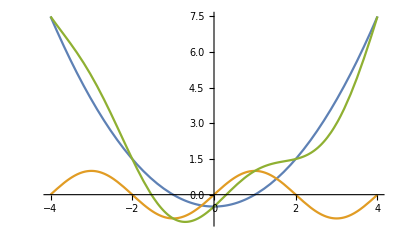

```mathematica
Plot[{(x^2-1)/2, g[x],f[x]}, {x, -4, 4}]
```

```mathematica
f[x]
```

1/2 (-1+x^2)+Sin[(π x)/2]

```mathematica
f[x+1]+f[x-1]//Simplify
```

x^2

```mathematica
(* Another: f(x f(y))= f(x y) + x, {x, y} ∈ Reals, independent variables *)
```

```mathematica
$Assumptions={x, y}∈Reals;
```

```mathematica
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]
f[x, 2]
```

a[0]+x a[1]+x^2 a[2]

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x f[y, n], n]==f[x y,n] + x,x]},{#,Length@#}&@sol]
```

```mathematica
sol[1]//Simplify
```

{{{a[0]→y+1/a[1]-y a[1]}},1}

```mathematica
f[x, 1]/.sol[1][[1]][[1]]
```

x a[1]+(1+y a[1]-y a[1]^2)/a[1]

```mathematica
(* Now we need to determine the value of the coefficient that makes y disappear in all cases (so that it can be an independent variable) *)
Solve[x a[1]+(1+y a[1]-y a[1]^2)/a[1]==x a[1]+1, a[1]]//Simplify
```

{{a[1]→1},{a[1]→-1/y}}

```mathematica
(* So, a[1] has to be 1 (the only value that's truly independent of y) *)
f[x_]:= x a[1]+(1+y a[1]-y a[1]^2)/a[1]/.a[1]-> 1//Simplify
f[x]
```

1+x

```mathematica
(* A related one (with y = f(x)): f(x f(f(x))) = f(x f(x)) + x *)
```

```mathematica
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]
f[x, 2]
```

a[0]+x a[1]+x^2 a[2]

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x f[f[x,n], n], n]==f[x f[x,n],n] + x,x]},{#,Length@#}&@sol]
```

```mathematica
sol[1]//Simplify
```

{{{a[0]→1,a[1]→1}},1}

```mathematica
f[x, 1]/.sol[1][[1]]
```

{1+x}

```mathematica
(* gives the solution directly(!) *)
f[x_]:= x+1
```

```mathematica
f[x f[f[x]]]==f[x f[x]] + x//Simplify
```

True

```mathematica
sol[2]//Simplify
```

{{{a[1]→1,a[2]→0,a[0]→1},{a[1]→1,a[2]→0,a[0]→1}},2}

```mathematica
(* same solution. *)
sol[3]
```

$Aborted

```mathematica
(* Let's explore rational functions: *)
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]/Total@Array[b[#] x^#&,n+1,0]
f[x, 2]
```

(a[0]+x a[1]+x^2 a[2])/(b[0]+x b[1]+x^2 b[2])

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x f[f[x,n], n], n]==f[x f[x,n],n] + x,x]},{#,Length@#}&@sol]
```

```mathematica
sol1 = sol[1]//Simplify
```

{{{b[1]→0,b[0]→0},{b[1]→0,b[0]→0},{a[0]→0,a[1]→0,b[0]→0},{a[0]→0,a[1]→0,b[0]→0},{a[1]→0,a[0]→0,b[0]→0},{a[1]→0,a[0]→0,b[0]→0},{a[1]→b[0],a[0]→b[0],b[1]→0},{a[1]→-b[0],a[0]→-b[0],b[1]→b[0]},{a[1]→-b[0],a[0]→-b[0]^2/b[1]}},9}

```mathematica
Table[f[x,1]/.sol1[[1]][[n]], {n, 1, sol1[[2]]}]//FullSimplify
```

{ComplexInfinity,ComplexInfinity,0,0,0,0,1+x,-1,-b[0]/b[1]}

```mathematica
f[x_]:= 1+x
f[x f[f[x]]]==f[x f[x]] + x//Simplify
```

True

```mathematica
f[x_]:= -1
f[x f[f[x]]]==f[x f[x]] + x//Simplify
```

x==0

```mathematica
sol2 = sol[2]//Simplify
```

$Aborted

```mathematica
(* Another: f(x y))= f(x) f(y), {x, y} ∈ Reals, independent variables *)
```

```mathematica
$Assumptions={x, y}∈Reals;
```

```mathematica
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]
f[x, 2]
```

a[0]+x a[1]+x^2 a[2]

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x y, n]==f[x,n] f[y,n],{x,y}]},{#,Length@#}&@sol]
```

```mathematica
sol1=sol[1]//Simplify
```

{{{a[0]→0,a[1]→0},{a[0]→0,a[1]→1},{a[0]→1,a[1]→0}},3}

```mathematica
Table[f[x,1]/.sol1[[1]][[n]], {n, 1, sol1[[2]]}]//FullSimplify
```

{0,x,1}

```mathematica
f[x_]:= 0
```

```mathematica
f[x y]== f[x]f[y]
```

True

```mathematica
f[x_]:= x
```

```mathematica
f[x y]== f[x]f[y]
```

True

```mathematica
f[x_]:= 1
```

```mathematica
f[x y]== f[x]f[y]
```

True

```mathematica
sol2=sol[2]//Simplify
```

{{{a[0]→0,a[1]→0,a[2]→0},{a[0]→0,a[1]→0,a[2]→1},{a[0]→0,a[1]→1,a[2]→0},{a[0]→1,a[1]→0,a[2]→0}},4}

```mathematica
Table[f[x,2]/.sol2[[1]][[n]], {n, 1, sol2[[2]]}]//FullSimplify
```

{0,x^2,x,1}

```mathematica
f[x_]:= x^2
```

```mathematica
f[x y]==f[x]f[y]
```

True

```mathematica
sol3=sol[3]//Simplify
```

{{{a[0]→0,a[1]→0,a[2]→0,a[3]→0},{a[0]→0,a[1]→0,a[2]→0,a[3]→1},{a[0]→0,a[1]→0,a[2]→1,a[3]→0},{a[0]→0,a[1]→1,a[2]→0,a[3]→0},{a[0]→1,a[1]→0,a[2]→0,a[3]→0}},5}

```mathematica
Table[f[x,3]/.sol3[[1]][[n]], {n, 1, sol3[[2]]}]//FullSimplify
```

{0,x^3,x^2,x,1}

```mathematica
(* So, all "pure" polynomials work *)
```

```mathematica
(* Let's explore rational functions: *)
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]/Total@Array[b[#] x^#&,n+1,0]
f[x, 2]
```

(a[0]+x a[1]+x^2 a[2])/(b[0]+x b[1]+x^2 b[2])

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x y, n]==f[x,n] f[y,n],{x,y}]},{#,Length@#}&@sol]
```

```mathematica
sol1=sol[1]//Simplify
```

{{{a[0]→0,a[1]→0},{a[0]→b[0],a[1]→b[1]},{b[1]→0,b[0]→0},{a[0]→0,a[1]→b[0],b[1]→0},{a[0]→0,a[1]→b[1],b[0]→0},{a[0]→b[0],a[1]→0,b[1]→0},{a[0]→b[0],a[1]→0,b[1]→0},{a[0]→b[0],a[1]→0,b[1]→0},{a[0]→b[1],a[1]→0,b[0]→0},{a[1]→b[1],a[0]→0,b[0]→0},{b[0]→0,b[1]→a[1],a[0]→0}},11}

```mathematica
Table[f[x,1]/.sol1[[1]][[n]], {n, 1, sol1[[2]]}]//FullSimplify//DeleteDuplicates
```

{0,1,ComplexInfinity,x,1/x}

```mathematica
sol2=sol[2]//Simplify;
```

```mathematica
Table[f[x,2]/.sol2[[1]][[n]], {n, 1, sol2[[2]]}]//FullSimplify//DeleteDuplicates
```

{0,1,ComplexInfinity,x,x^2,1/x,1/x^2}

```mathematica
(* Another: f(x) + f((x-1)/x) = 1+x, x ≠ 0, 1 *)
```

```mathematica
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]/Total@Array[b[#] x^#&,n+1,0]
f[x, 2]
```

(a[0]+x a[1]+x^2 a[2])/(b[0]+x b[1]+x^2 b[2])

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x, n]+f[(x-1)/x,n]==1+x,x]},{#,Length@#}&@sol]
```

```mathematica
sol1=sol[1]
```

{{{b[1]→0,b[0]→0},{b[1]→0,b[0]→0}},2}

```mathematica
Table[f[x,1]/.sol1[[1]][[n]], {n, 1, sol1[[2]]}]//FullSimplify//DeleteDuplicates
```

{ComplexInfinity}

```mathematica
sol2=sol[2]
```

{{{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0},{b[0]→0,b[1]→0,b[2]→0}},18}

```mathematica
Table[f[x,2]/.sol2[[1]][[n]], {n, 1, sol2[[2]]}]//FullSimplify//DeleteDuplicates
```

{ComplexInfinity}

```mathematica
sol3=sol[3]
```

{{{b[0]→0,b[1]→0,b[2]→0,b[3]→0},{b[0]→0,b[1]→0,b[2]→0,b[3]→0},{b[0]→0,b[1]→0,b[2]→0,b[3]→0},{b[0]→0,b[1]→0,b[2]→0,b[3]→0},{b[0]→0,b[1]→0,b[2]→0,b[3]→0},{b[0]→0,b[1]→0,b[2]→0,b[3]→0},{b[0]→0,b[1]→0,b[2]→0,b[3]→0},{b[0]→0,b[1]→0,b[2]→0,b[3]→0},{b[0]→0,b[1]→0,b[2]→0,b[3]→0},{b[1]→0,b[0]→0,b[2]→0,b[3]→0},{a[0]→-b[2]/2,a[1]→0,a[2]→-b[2]/2,a[3]→b[2]/2,b[1]→-b[2],b[0]→0,b[3]→0},{a[0]→-b[2]/2,a[1]→0,a[2]→-b[2]/2,a[3]→b[2]/2,b[1]→-b[2],b[0]→0,b[3]→0}},12}

```mathematica
Table[f[x,3]/.sol3[[1]][[n]], {n, 1, sol3[[2]]}]//FullSimplify//DeleteDuplicates
```

{ComplexInfinity,(1+x^2-x^3)/(2 x-2 x^2)}

```mathematica
f[x_]:= (1+x^2-x^3)/(2 x-2 x^2)
```

```mathematica
f[x]+f[(x-1)/x]//FullSimplify
```

1+x

```mathematica
f[x]//Expand
```

1/(2 x-2 x^2)+x^2/(2 x-2 x^2)-x^3/(2 x-2 x^2)

```mathematica
Subscript[f, RazimanTV][x_]:= x/2-1/(2(x-1))+1/(2x)
```

```mathematica
Subscript[f, RazimanTV][x]+Subscript[f, RazimanTV][(x-1)/x]//FullSimplify
```

1+x

```mathematica
f[x]
```

(1+x^2-x^3)/(2 x-2 x^2)

```mathematica
Subscript[f, RazimanTV][x]//Together
```

(-1-x^2+x^3)/(2 (-1+x) x)

```mathematica
Subscript[f, RazimanTV][x]==f[x]//Reduce
```

True

```mathematica
(* Another: f(√(x^2 + y^2)) = f(x) + f(y), f(1) = 1 , {x, y} ∈ Reals *)
```

```mathematica
$Assumptions={x, y}∈Reals;
```

```mathematica
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]
f[x, 2]
```

a[0]+x a[1]+x^2 a[2]

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[√(x^2+y^2), n]==f[x,n]+f[y,n],{x,y}]},{#,Length@#}&@sol]
```

```mathematica
sol1=sol[1]
```

{{{a[0]→0,a[1]→0}},1}

```mathematica
sol2=sol[2]
```

{{{a[0]→0,a[1]→0}},1}

```mathematica
Table[f[x,2]/.sol2[[1]][[n]], {n, 1, sol2[[2]]}]//FullSimplify//DeleteDuplicates
```

{x^2 a[2]}

```mathematica
f[x_]:= a x^2
```

```mathematica
f[√(x^2+y^2)]==f[x]+f[y]//FullSimplify
```

True

```mathematica
(* But f(1) = 1, so: *)
f[√(x^2+y^2)]==f[x]+f[y]&&f[1]==1//Reduce
```

a==1

```mathematica
f[x_]:= a x^2/.a->1
f[x]
```

x^2

```mathematica
(* Another: 2 f(x) - x f((2 x + 3)/(x-2)) = 3 *)
```

```mathematica
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]/Total@Array[b[#] x^#&,n+1,0]
f[x, 2]
```

(a[0]+x a[1]+x^2 a[2])/(b[0]+x b[1]+x^2 b[2])

```mathematica
sol[n_]:=With[{sol=SolveAlways[2f[x, n]-x f[(2x+3)/(x-2),n]==3,x]},{#,Length@#}&@sol]
```

```mathematica
sol1=sol[1]
```

{{{b[0]→0,b[1]→0}},1}

```mathematica
Table[f[x,1]/.sol1[[1]][[n]], {n, 1, sol1[[2]]}]//FullSimplify//DeleteDuplicates
```

{ComplexInfinity}

```mathematica
sol2=sol[2]
```

{{{b[0]→0,b[1]→0,b[2]→0},{a[2]→-(3 b[2])/2,a[1]→0,a[0]→6 b[2],b[0]→4 b[2],b[1]→-b[2]/2}},2}

```mathematica
Table[f[x,2]/.sol2[[1]][[n]], {n, 1, sol2[[2]]}]//FullSimplify//DeleteDuplicates
```

{ComplexInfinity,-(3 (-4+x^2))/(8+x (-1+2 x))}

```mathematica
f[x_]:= (3 (-4+x^2))/(8+x (-1+2 x))
```

```mathematica
f[x]//Expand
```

-12/(8+x (-1+2 x))+(3 x^2)/(8+x (-1+2 x))

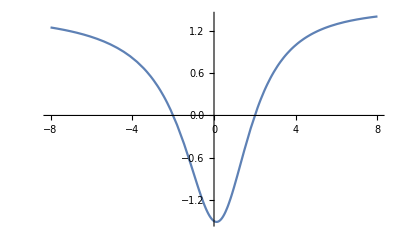

```mathematica
Plot[-12/(8+x (-1+2 x))+(3 x^2)/(8+x (-1+2 x)),{x,-8,8}]
```

```mathematica
(* Another one f(f(x)) = x + 1 *)
```

```mathematica
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]
f[x, 2]
```

a[0]+x a[1]+x^2 a[2]

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[f[x,n],n]==x+1,x]},{#,Length@#}&@sol]
```

```mathematica
sol[1]//Simplify
```

{{{a[1]→1,a[0]→1/2}},1}

```mathematica
f[x, 1]/.sol[1][[1]]
```

{1/2+x}

```mathematica
f[x_]:= x+1/2
```

```mathematica
f[f[x]]==x+1
```

True

```mathematica
(* Let's try this one f(f(x)f(y)) = f(x y) *)
```

```mathematica
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]
f[x, 2]
```

a[0]+x a[1]+x^2 a[2]

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[f[x, n] f[y,n],n]==f[x y,n],{x,y}]},{#,Length@#}&@sol]
```

```mathematica
sol[1]
```

{{{a[0]→0,a[1]→-1},{a[0]→0,a[1]→1},{a[1]→0}},3}

```mathematica
sol[1]
```

{{{a[0]→0,a[1]→-1},{a[0]→0,a[1]→1},{a[1]→0}},3}

```mathematica
fs=f[x,1]/.sol[1][[1]]
```

{-x,x,a[0]}

```mathematica
f1[x_]:= fs[[1]]
f2[x_]:= fs[[2]]
f3[x_]:= fs[[3]]
```

```mathematica
f1[f1[x]f1[y]]==f1[x y]
f2[f2[x]f2[y]]==f2[x y]
f3[f3[x]f3[y]]==f3[x y]
```

True

True

True

```mathematica
(* Another: f(x)^2 - f(-x)^2 == 4x *)
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]
f[x, 1]
```

a[0]+x a[1]

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x,n]^2-f[-x,n]^2==4x,x]},{#,Length@#}&@sol]
```

```mathematica
s=sol[1]
```

{{{a[0]→1/a[1]}},1}

```mathematica
f[x, 1]/.s[[1]][[1]]//Simplify
```

1/a[1]+x a[1]

```mathematica
(* Let's see: *)
(1/a+a x)^2-(1/a-a x)^2//FullSimplify
```

4 x

```mathematica
(* Another: f((x-3)/(x+1))+f((x+3)/(1-x))==2x : *)
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]/Total@Array[b[#] x^#&,n+1,0]
f[x, 3]
```

(a[0]+x a[1]+x^2 a[2]+x^3 a[3])/(b[0]+x b[1]+x^2 b[2]+x^3 b[3])

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[(x-3)/(x+1),n]+f[(x+3)/(1-x),n]==2x,x]},{DeleteDuplicates@#,Length@#}&@sol]
```

```mathematica
s3=sol[3]
```

{{{b[0]→0,b[1]→0,b[2]→0,b[3]→0},{a[0]→0,a[2]→0,a[1]→-7 b[2],a[3]→-b[2],b[1]→0,b[3]→0,b[0]→-b[2]}},20}

```mathematica
s3[[1]][[2]]
```

{a[0]→0,a[2]→0,a[1]→-7 b[2],a[3]→-b[2],b[1]→0,b[3]→0,b[0]→-b[2]}

```mathematica
f[x, 3]/.s3[[1]][[2]]//Simplify
```

-(x (7+x^2))/(-1+x^2)

```mathematica
(* Another: f(x/(x-1))==2f(x)+x^2: *)
f[x_,n_]:=Total@Array[a[#] x^#&,n+1,0]/Total@Array[b[#] x^#&,n+1,0]
f[x, 3]
```

(a[0]+x a[1]+x^2 a[2]+x^3 a[3])/(b[0]+x b[1]+x^2 b[2]+x^3 b[3])

```mathematica
sol[n_]:=With[{sol=SolveAlways[f[x/(x-1),n]==2f[x,n]+x^2,x]},{DeleteDuplicates@#,Length@#}&@sol]
```

```mathematica
s4=sol[4]
```

{{{b[0]→0,b[1]→0,b[2]→0,b[3]→0,b[4]→0},{a[4]→-(2 b[0])/3,a[3]→(4 b[0])/3,a[2]→-b[0],a[1]→0,a[0]→0,b[4]→0,b[3]→0,b[2]→b[0],b[1]→-2 b[0]}},50}

```mathematica
f[x, 4]/.s4[[1]][[2]]//FullSimplify//Expand//FactorTerms//Factor
```

-(x^2 (3-4 x+2 x^2))/(3 (-1+x)^2)

```mathematica
Reduce[(f[x, 4]/.s4[[1]][[2]]//FullSimplify)==1/3(-2-1/(-1+x)^2)x^2]
```

True